```mathematica
Integrate[Sin[k r]k/((k^2+mu)^2)^(1/2),{k,0,Infinity}]
```

If[r∈Reals&&(mu∈Reals||Re[mu]==0)&&(Im[√mu]≥0||Re[√mu]≠0)&&(Im[√mu]≤0||Re[√mu]≠0)&&(mu∈Reals||Im[mu]^2≤0||√Re[mu]==0||-ⅈ √Re[mu]≥0),(ⅇ^(-√mu Abs[r]) π r)/(2 Abs[r]),Integrate[(k Sin[k r])/(√((k^2+mu)^2)),{k,0,∞},Assumptions→r∉Reals||(mu∉Reals&&Re[mu]≠0)||(√mu∉Reals&&Re[√mu]==0)]]

```mathematica
Simplify[%%,{r>0,mu>0}]
```

1/2 ⅇ^(-√mu r) π

```mathematica
Sin[k r]k/((k^2+mu)^2)^(1/2)
```

(k Sin[k r])/(√((k^2+mu)^2))

```mathematica
f[k_]:=k^2/((k^2+kp^2)^2(((k^2-kmu^2)^2+kD^2)^(1/2)));
ff[k_]:=k^2/((kp^4)(((k^2-kmu^2)^2+kD^2)^(1/2)));
```

```mathematica
f[k]/.cond
```

k^2/((10000+k^2) √(1+(100+k^2)^2))

```mathematica
cond={kmu->-10I,kp->100,kD->1}
```

{kmu→-10 ⅈ,kp→100,kD→1}

```mathematica
D[f[k],k]
```

-(2 k^3)/(√(kD^2+(k^2-kmu^2)^2) (k^2+kp^2)^2)-(2 k^3 (k^2-kmu^2))/((kD^2+(k^2-kmu^2)^2)^(3/2) (k^2+kp^2))+(2 k)/(√(kD^2+(k^2-kmu^2)^2) (k^2+kp^2))

```mathematica
Simplify[%]
```

(2 k (-k^6+k^4 kmu^2-k^2 kmu^2 kp^2+(kD^2+kmu^4) kp^2))/((k^4+kD^2-2 k^2 kmu^2+kmu^4)^(3/2) (k^2+kp^2)^2)

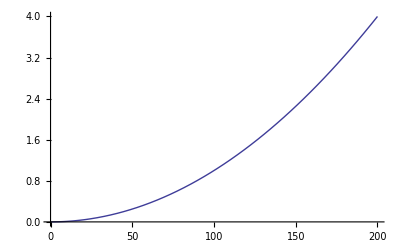

```mathematica
Plot[((ff[k]-f[k])/f[k])/.cond,{k,0,200},PlotRange->Full]
```

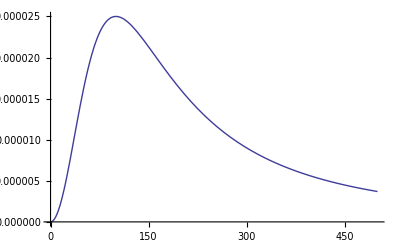

```mathematica
Plot[{f[k]*(k k -kmu kmu)}/.cond,{k,0,500},PlotRange->Full]
```

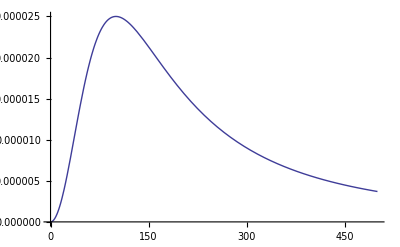

```mathematica
Plot[{k^2/(k k +kp kp)^2}/.cond,{k,0,500},PlotRange->Full]
```

```mathematica
f[k]*(k k -kmu kmu)/.cond
```

(k^2 (100+k^2))/((10000+k^2)^2 √(1+(100+k^2)^2))

```mathematica
NIntegrate[f[k]/.cond,{k,0,Infinity}]
```

0.01428

```mathematica
f2[k_]:=kp/(k^2+kp^2)
```

```mathematica
Integrate[(f2[k])^2*k k,{k,0,Infinity}]
```

kp^2 If[Re[kp]>0,π/(4 kp),Integrate[k^2/((k^2+kp^2)^2),{k,0,∞},Assumptions→Re[kp]≤0]]

```mathematica
f2[k]
```

kp/(k^2+kp^2)

```mathematica
Integrate[1/(k^2+kp^2)^2,{k,0,Infinity}]
```

If[Re[kp^2]≥0||kp^2∉Reals,1/4 (1/kp^2)^(3/2) π,Integrate[1/((k^2+kp^2)^2),{k,0,∞},Assumptions→Re[kp^2]<0&&kp^2∈Reals]]

```mathematica
Integrate[k^2/(k^2+kp^2)^2,{k,0,Infinity}]
```

If[Re[kp]>0,π/(4 kp),Integrate[k^2/((k^2+kp^2)^2),{k,0,∞},Assumptions→Re[kp]≤0]]

```mathematica
Integrate[k^2/((k^2-1)^2+dt^2)^(1/2),{k,0,kc}]
```

$Aborted

```mathematica
Integrate[1/(k^2+dt^2)^(1/2),{k,0,kc}]
```

If[Im[dt/kc]≥1||1+Im[dt/kc]≤0||dt/kc∈Reals||Re[dt/kc]≠0,-1/2 Log[dt^2]+Log[kc+√(dt^2+kc^2)],Integrate[1/(√(dt^2+k^2)),{k,0,kc},Assumptions→!(Im[dt/kc]≥1||1+Im[dt/kc]≤0||dt/kc∈Reals||Re[dt/kc]≠0)]]

```mathematica
Simplify[%,{dt>0,kc>0}]
```

Log[(kc+√(dt^2+kc^2))/dt]

```mathematica
k^2/((k^2-1)^2+dt^2)^(1/2)
```

k^2/(√(dt^2+(-1+k^2)^2))

```mathematica
fk[k_]:=k^2/((k^2-1)^2+dt^2)^(1/2)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {0.9887041937466647`}. NIntegrate obtained 105.791 and 0.595897 for the integral and error estimates.

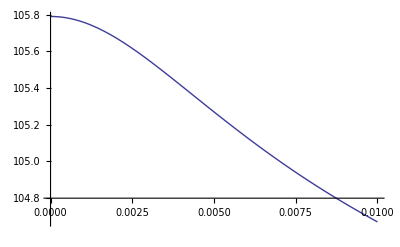

```mathematica
Plot[NIntegrate[fk[k],{k,0,100}],{dt,0,0.01}]
```

```mathematica
Integrate[fk[k]/.dt->0,{k,0,k1}]
```

∫_0^k1 k^2/(√((-1+k^2)^2))ⅆk

```mathematica
Simplify[%]
```

((-1+k^2) (2 k+Log[1-k]-Log[1+k]))/(2 √((-1+k^2)^2))

Integrate::idiv: Integral of k^2/Abs[-1 + k^2] does not converge on {0, 10.001838571428571`}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {0.9964323339306329`}. NIntegrate obtained 16.92 and 0.682402 for the integral and error estimates.

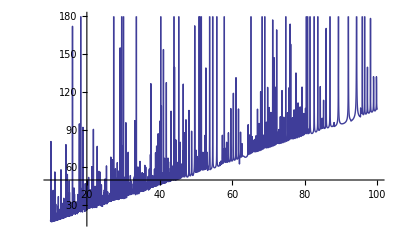

```mathematica
Plot[%,{k1,10,100}]
```

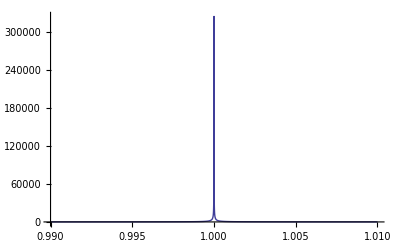

```mathematica
Plot[fk[k]/.dt->0,{k,0.99,1.01},PlotRange->All]
```